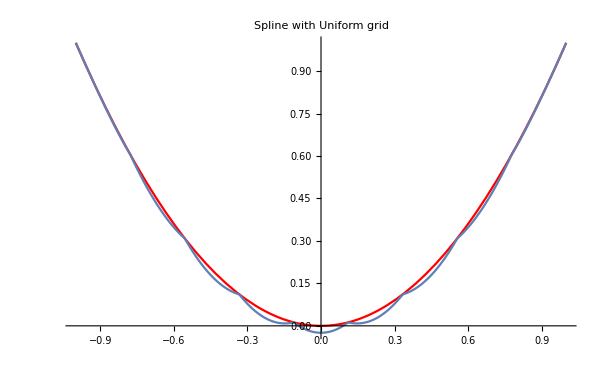

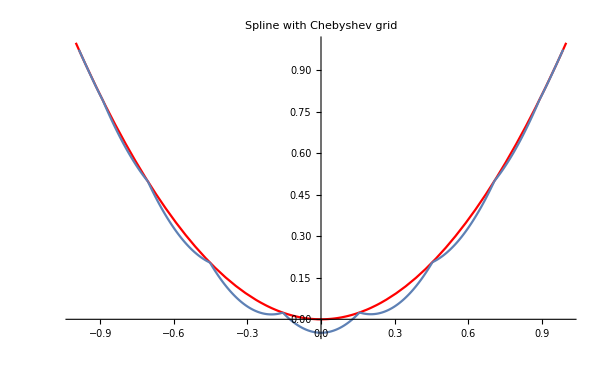

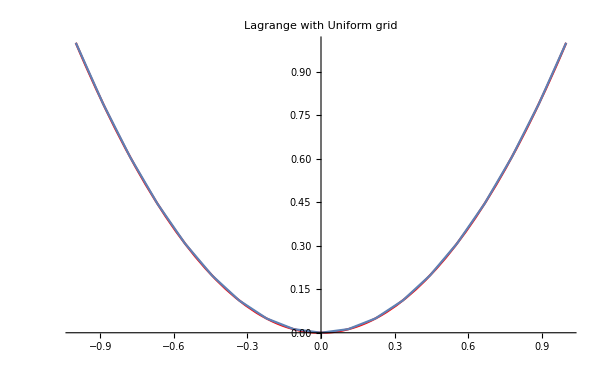

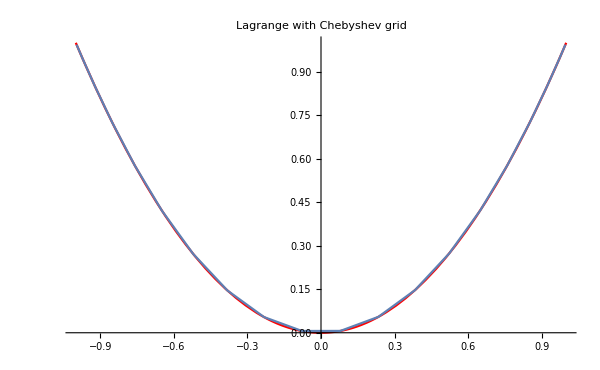

```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];
func[x] = x*x;
plotf = Plot[func[x],{x,-1,1},PlotStyle->Red];
unilist = ReadList["uniform.txt", Number, RecordLists->True];
cheblist = ReadList["chebysh.txt", Number, RecordLists->True];
unispline= ReadList["unispline.txt", Number, RecordLists->True];
chebspline= ReadList["chebspline.txt", Number, RecordLists->True];
n1=unispline[[1,1]];
n2=chebspline[[1,1]];
listplot1={};
listplot2={};

For[i=1,i<n1,i++,
spline=unispline[[i+1,1]]+unispline[[i+1,2]]*(x-unilist[[1,i]])+unispline[[i+1,3]]*(x-unilist[[1,i]])^2+unispline[[i+1,4]]*(x-unilist[[1,i]])^3;
plot=Plot[spline==0,{x,unilist[[1,i]],unilist[[1,i+1]]}];
listplot1=Append[listplot1,plot];
]
Show[plotf,listplot1,PlotRange->All,ImageSize->600,PlotLabel->"Spline with Uniform grid"]

For[i=1,i<n2,i++,
spline=chebspline[[i+1,1]]+chebspline[[i+1,2]]*(x-cheblist [[1,i]])+chebspline[[i+1,3]]*(x-cheblist [[1,i]])^2+chebspline[[i+1,4]]*(x-cheblist [[1,i]])^3;
plot=Plot[spline==0,{x,cheblist [[1,i]],cheblist [[1,i+1]]}];
listplot2=Append[listplot2,plot];
]
Show[plotf,listplot2,PlotRange->All,ImageSize->600,PlotLabel->"Spline with Chebyshev grid"]

unipoints = ReadList["uni_points.txt", Number, RecordLists->True];
plotu = ListLinePlot[Partition[Riffle[unipoints[[1]], unipoints[[2]]],2]];
Show[plotf, plotu, PlotRange->All,PlotLabel->"Lagrange with Uniform grid"]
chebpoints = ReadList["cheb_points.txt", Number, RecordLists->True];
plotc= ListLinePlot[Partition[Riffle[chebpoints[[1]], chebpoints[[2]]],2]];
Show[plotf, plotc, PlotRange->All,PlotLabel->"Lagrange with Chebyshev grid"]
```